# Arc routing with the Bridges of Königsberg

Peter Burbery

Abstract

## The bridges of Königsberg riddle

In 1736, the residents of Königsberg asked this question. Is it possible to walk across every bridge once before crossing any bridge more than once in the this picture? Backtracking across a bridge you have already crossed is not allowed, you can only cross bridges you have not walked across. You also have to return to the island you started at.

-Graphics-

Leonard Euler converted this into a graph theory question. A graph is made up of vertices (singular vertex) that form a set V and a set of edges between vertices named E.

Create a graph 𝒢 composed of a set of vertices 𝒱 and a set of undirected edges ℰ. The vertices are named ℒ, ℳ, ℛ, and ℬ for the left, middle, right, and bottom islands.

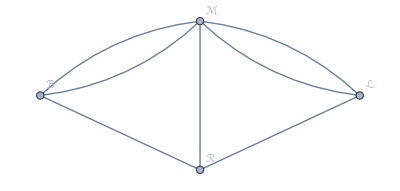

```mathematica
𝒢=Graph[
𝒱={ℒ,ℳ,ℛ,ℬ},
ℰ={ℬ<->ℳ,ℬ<->ℳ,ℒ<->ℳ,ℒ<->ℳ,ℳ<->ℛ,ℛ<->ℒ,ℛ<->ℬ},
VertexLabels->Automatic]
```

We can simplify the question by ignoring the dimensions of the problem and the locations of the bridges. Euler's paper on the bridges of Konigsberg was the first graph theory problem, the first arc routing theorem, and the first topological theorem.

A walk is a set of adjacent edges that traverses a graph. A walk is closed if it stops and starts at the same vertex in a graph or node in a network. A trail is a walk that does not repeat edges. A path is a walk that does not repeat vertices or edges. A circuit is a closed trail, or a walk that starts and ends at the same vertex without repeating edges. A cycle is a walk that does not repeat vertices or edges. A tour is a closed trail. Paths and graphs are important types of graphs as well.

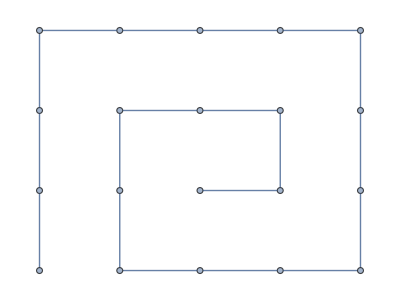

```mathematica
PathGraph[Range[20]]
```

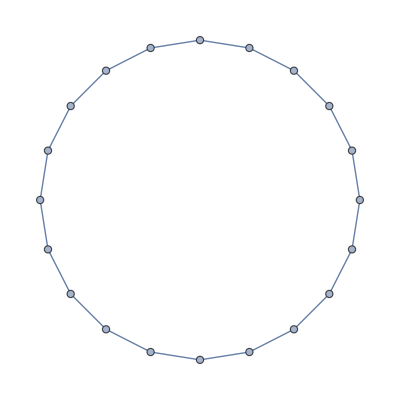

```mathematica
CycleGraph[20]
```

Euler noticed that if a graph has exactly two odd-degree vertices, a walk across across every bridge is possible but it must start and end at the two odd-degree vertices. The bridges of Königsberg have more than two odd degree vertices, therefore there is no walk that can cross every bridge at least once. If there were only two odd degree vertices, the graph would be Semi-Eulerian. The Handshaking lemma is an important proof in graph theory that states that there is always an even number of odd-degree vertices in a graph.

Group the vertices by whether they have an even or odd vertex degree.

```mathematica
GroupBy[𝒱,EvenQ[VertexDegree[𝒢,#]]&]
```

<|False→{ℒ,ℳ,ℛ,ℬ}|>

A graph with only even degree vertices and no odd degree vertices is Eulerian, or unicursal. An Eulerian graph has at least one Eulerian cycle.

Prove the graph is not Eulerian.

```mathematica
EulerianGraphQ[𝒢]
```

False

Verify there are no Eulerian cycles

```mathematica
FindEulerianCycle[𝒢]
```

{}

The graph can be Eulerized to form an augmented graph that is Eulerian with Christofides algorithm.

Christofides Algorithm can be applied to any graph that obeys the triangle inequality, which states that ‖x+y‖<=‖x‖+‖y‖ for vectors x and y in metric space.

Create a map of modern day Königsberg, which is no longer an independent city of Prussia. Königsberg was incorporated into Kaliningrad as a Russian city and the some of the bridges from Euler's time were bombed during World War II. I will use geodesic distance for an equirectangular projection with GeographPlot.

```mathematica
kantIsland=GeoMarker[{54.7065,20.51013},Text["ℳ",Background->LightGray],"Color"->Red,"Scale"->100];
top=GeoMarker[{54.7085,20.510038},Text["ℒ",Background->LightGray],"Color"->Red];
right=GeoMarker[{54.705719,20.515416},Text["ℛ",Background->LightGray],"Color"->Red];
lower=GeoMarker[{54.703798,20.5094},Text["ℬ",Background->LightGray],"Color"->Red];
rm=GeoGraphics[{kantIsland,top,right,lower,GeoPosition[{54.706583333333334,20.51013888888889}]},GeoRange->Quantity[.5,"Kilometers"],GeoBackground->"StreetMap",ImageSize->Full]
```

-Graphics-

```mathematica
GeoCoordinates=GeoPosition/@{{54.7065,20.51013},{54.703798,20.5094},{54.705719,20.515416},{54.7085,20.510038}}
Geo𝒢=VertexReplace[𝒢,Thread[VertexList[𝒢]->GeoCoordinates]];
Geo𝒢=Graph[Geo𝒢,EdgeWeight->Thread[EdgeList[Geo𝒢]->(GeoDistance[First[#],Last[#]]&/@EdgeList[Geo𝒢])]];
GeoGraphPlot[Geo𝒢,VertexLabels->Thread[VertexList[Geo𝒢]->𝒱],EdgeLabels->"EdgeWeight",GeoRange->Quantity[0.5, "Kilometers"],ImageSize->Full]
```

{GeoPosition[{54.7065,20.5101}],GeoPosition[{54.7038,20.5094}],GeoPosition[{54.7057,20.5154}],GeoPosition[{54.7085,20.51}]}

-Graphics-

```mathematica
MatrixForm@Normal@WeightedAdjacencyMatrix[Geo𝒢]
```

(0 | 608.881 m | 351.657 m | 0
608.881 m | 0 | 442.86 m | 1050.06 m
351.657 m | 442.86 m | 0 | 464.771 m
0 | 1050.06 m | 464.771 m | 0)

```mathematica
FindGraphIsomorphism[𝒢,Geo𝒢]
```

{<|ℒ→GeoPosition[{54.7065,20.5101}],ℳ→GeoPosition[{54.7038,20.5094}],ℛ→GeoPosition[{54.7057,20.5154}],ℬ→GeoPosition[{54.7085,20.51}]|>}

```mathematica
EdgeCount[𝒢]
```

7

## Konigsberg 2000s

(Modern Day Königsberg)

The city of Königsberg has been incorporated into the Russian city of Kalingrad and two of the bridges have been destroyed by bombing during World War II.

(The city was not incorporated by the city of kalingrad, it was renamed)
Rewrite:
The city is now named Kalingrad, two of the bridges have been destroyed by bombing during World War II. They were replaced with 1 Highway and 3 new bridges increasing number of availible edges.

Geographic visualization of modern day Königsberg.

(Zoom in the map(decrease the GeoRange)

Make a new graph of Königsberg today.

(Kaliningrad - Not Königsberg)

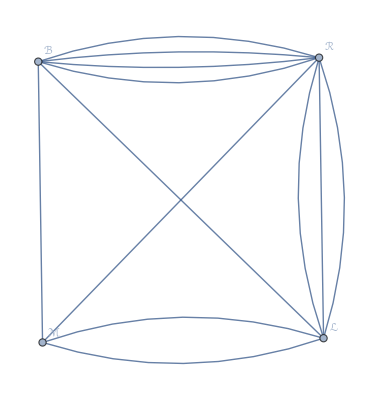

```mathematica
Königsberg2022graph=Graph[Königsberg2022vertices={ℒ,ℳ,ℛ,ℬ},Königsberg2022edges={ℬ<->ℒ,ℒ<->ℳ,ℒ<->ℳ,ℳ<->ℬ,ℳ<->ℛ,ℬ<->ℛ,ℬ<->ℛ,ℬ<->ℛ,ℛ<->ℒ,ℛ<->ℒ,ℛ<->ℒ,ℬ<->ℛ},VertexLabels->Automatic]
```

(Modern Day Königsberg)

```mathematica
GroupBy[Königsberg2022vertices,EvenQ[VertexDegree[Königsberg2022graph,#]]&]
```

<|True→{ℒ,ℳ,ℛ,ℬ}|>

(EulerianQ?)

```mathematica
EulerianGraphQ[Königsberg2022graph]
```

True

If you zoom out enough on the map, the bridges of Königsberg can now be crossed in an Eulerian walk!

(You could say "Modern day engineers heeded Euler's advice and made sure you could take a Eulerian walk!")

## Making a graph Eulerian

To make a graph Eulerian, you pair up the odd vertices and randomly match them. If there are weights on the graph, for example if the bridges have distances associated with them, the matching has to minimal.

(This is a different problem from above, you should prefece this section)
"If given a random graph with some number of odd vertices, we can attempt to Eulerize the graph by matching the odd vertices."
(Is this the minimum number of edges needed?)

(Describe how the function works)

```mathematica
ClearAll[EulerizeGraph]
EulerizeGraph[graph_?ConnectedGraphQ]:=NestWhile[(x↦EdgeAdd[x,UndirectedEdge[First[#],Last[#]]&@First@TakeDrop[Select[VertexList[x],OddQ[VertexDegree[x,#]]&],2]]),graph,!EulerianGraphQ[#]&]
```

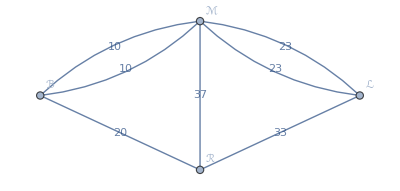

```mathematica
KönigsbergGraphWithWeightedEdges=Graph[{ℒ,ℳ,ℛ,ℬ},edgesWeighted={ℬ<->ℳ,ℬ<->ℳ,ℒ<->ℳ,ℒ<->ℳ,ℳ<->ℛ,ℛ<->ℒ,ℛ<->ℬ},VertexLabels->Automatic,EdgeWeight->RandomInteger[{1,54},7],EdgeLabels->"EdgeWeight"]
```

(Lets Eulerize Königsberg in 1736)

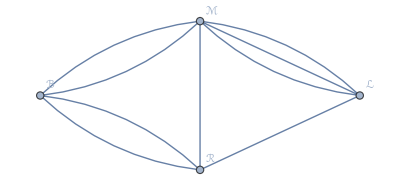

```mathematica
EulerizeGraph[Königsberg1736graph]
```

(Not sure if this works)

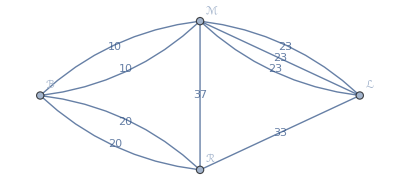

```mathematica
EulerizeGraph[KönigsbergGraphWithWeightedEdges]
```